## Axon-Hillock Analysis

We found that using a delayed inverter, although it creates nice looking oscillatory waveforms, operates too slow and doesn’t resolve the linearity problem we were seeing with the starved inverters.  The linearity problem we were seeing was that the period of an oscillation didn’t vary linearly with the input current (or throttling current), I_in.  As such, Ben suggested that we look into the Axon-Hillock circuit that he uses in the pulse extender, which comes from Carver’s book.  This notebook will have any of the Mathematica based analysis that we perform on this AH circuit.

Background/Setup

In this sub-chapter, I try to define the situation and how we are performing our analysis.  The reference circuit for my analysis is shown below.

## Capacitor divider background

The first thing we need to understand is how a capacitor divider circuit operates because the fundamental analysis of an axon-hillock circuit requires understanding the mechanism of the capacitor divider in the middle of the circuit, comprised of C_1 and C_2.

### Parallel Caps → Serial Caps

At time t=0, we can assume that the capacitor circuit switches from the first configuration below to the second configuration.  The first configuration is two capacitors in parallel and the second configuration is two capacitors in series (forming a capacitor divider).  What this implies is that when t=0, V_o goes from 0 to 1 (or from Gnd to V_dd).  V_o is named because it the voltage of the output node from this circuit.  The circuit’s output (V_o) forms an oscillatory square wave.

-Graphics-  →^(t=0)

Based on the basic circuit equation Q=C·V and the fact that two caps in parallel is the same as the one cap equal to the sum of the two cap’s capacitances, we know that when t<0, the overall charge across the circuit on the left is defined as follows:
	Q_0=(C_1+C_2)V_i 
where V_i is the initial voltage of V_c @ t=0.

At t=0, we know the circuit changes modes from the circuit on the left to the circuit on the right.  We assume this change happens near instantaneously.  Because of this we also know that Q_0=Q_1-Q_2, where Q_1 and Q_2 are the charges on the two capacitors individually, because the charge doesn’t escape instantaneously.  We also note that the charge for Q_2 is negative.  This is purely because the charges built up at V_c before t=0, are positive and the charges on the other side of the plate’s are negative.  At t=0, these positive charges are on the wrong side of the C_2’s plates and so there is, what appears to be, a negative charge across C_2.

We also know that the following equations are true for Q_1 and Q_2.
	Q_1=C_1·V_c
	Q_2=C_2·(V_dd-V_c)
As such, the following equations becomes the state of the circuit’s charge at t=0, because no charge can magically move/change/disappear in an instant.
	Q_0=Q_1-Q_2
	(C_1+C_2)V_i=C_1·V_c-C_2·(V_dd-V_c)
	(C_1+C_2)V_i=C_1·V_c- C_2·V_dd+C_2·V_c
	(C_1+C_2)V_i+C_2·V_dd=(C_1+C_2)V_c
	V_i+C_2/(C_1+C_2)·V_dd=V_c
	V_c=V_i+C_2/(C_1+C_2)·V_dd

V_c=V_i+ΔV
ΔV=C_2/(C_1+C_2)·V_dd

This essentially says that at t=0, the voltage at V_c will have a nearly instantaneous change equal to ΔV.  ΔV is equal to the capacitor divider ratio multiplied by V_dd.

### Serial Caps → Parallel Caps

Going the other way, if we assumed that at t=0, we started in the serial configuration, and then it switched instantaneously to the parallel configuration, as shown below, then the following math describes the circuit’s behavior.  This is the same as saying when V_o goes from 1 to 0 (or from V_dd to Gnd), the following math applies.

→^(t=0) -Graphics-

This math is essentially the same as the math above, except that anywhere it used to say V_i above, it should now say V_c in this math, and vice-versa.  This is because the initial condition V_i is the voltage at which the V_csits at t=0.  Then we want to see how V_c changes in the parallel circuit.
	Q_0=Q_1-Q_2
	(C_1+C_2)V_c=C_1·V_i-C_2·(V_dd-V_i)
	(C_1+C_2)V_c=C_1·V_i- C_2·V_dd+C_2·V_i
	(C_1+C_2)V_c=(C_1+C_2)V_i-C_2·V_dd
	V_c=V_i-C_2/(C_1+C_2)·V_dd

V_c=V_i-ΔV
ΔV=C_2/(C_1+C_2)·V_dd

### Summary of capacitor behavior

These two conclusions mean that the following equation is true, anytime the circuit switches between these two modes, depending on which way the circuit switches:

V_c=V_i±ΔV
ΔV=C_2/(C_1+C_2)·V_dd

## AH Circuit Derivation w/ no feedback

### Background and general equations

Now that we have an understanding of how the capacitor divider operates and a mathematical model of its behavior, we can analyze the AH circuit above.  The first thing to note is that the circuit has three inverters, denoted I_1, I_2, and I_3.  These inverters are drawn above using transistors PI_x and NI_x, where x is the number of the inverter.  There are also two transistors that serve as the “current sources”, P_1 and N_1.  These current sources determine how quickly the joint capacitors C_1 and C_2 charge or discharge.  In other words, the circuit can be described as having three main components: inverters, a capacitor divider (which changes behavior based on V_o’s voltage), and current sources.

When V_o switches, as a result of V_c crossing the inversion point of I_1, the capacitor divider will change between the two modes of the capacitor divider circuit analyzed in the previous section.  Also, when V_o switches, I_3, disables either PI_3 or NI_3, which changes the mode of the circuit from charging the caps to discharging the caps.  As such, the duration of this switching occurrence is determined by how quickly the caps charge/discharge.

For the purposes of the math below, we assume that V_c sits at some average value V_i, from which the ΔV switch occurs.  For durations t_lo and t_hi, the circuit will either charge or discharge depending whether or not V_o is low or high, respectively.  Said another way, when V_o is low, the circuit is charging, and when V_o is high, the circuit is discharging.

First we know from basic circuit’s equations that the following equation are true, where we need to define I, C, and dV/dt.
	I=C dV/dt
The voltage that we are changing over time is V_c, and therefore we are actually measuring the rate of change as follows:
	dV/dt=dV_c/dt
In this circuit, the rate of current that charges/discharges the capacitors can always be defined as follows (Note: The direction of current flow (whether it’s in to or out of the node V_c merely determines the fact that I is charging or discharging.  As such, I’ve made the generality that the only thing that matters is the sum of the two independent currents):
	I=I_P1+I_N1
Also, regardless of the mode that the circuit is in, we know that the change in the voltage (ΔV) is equal to the instantaneous jump that the capacitor divider moved.
	ΔV=C_2/(C_1+C_2)·V_dd
There is one main difference between the charging mode and discharging mode.  The difference is that I_P1 and I_N1 behave differently in the two modes.  The mathematical derivation for these two modes is defined below to calculate what t_lo and t_hi equal in each mode.

### Charging the capacitors

In the charging mode, we can assume a couple of the following things.  The first thing we assume is that V_o is set to GND or 0V.  This also implies that the capacitors are in a parallel configuration.  The second thing that follows from the first assumption is that V_s is equal to 1, because it is the inverted output of V_o.  The second assumption that we can make is that V_o and V_s transition instantaneously.  As such, when the circuit is charging the capacitors, the equivalent capacitance is equal to the sum of the two capacitors.
	C=C_1+C_2
We also know that when V_s=1, transistor P_1 forms a perfect current mirror with its bias and as such:
	I_P1=I_in		 (Note: we are assuming no mismatch in the transistors).
I_N1 on the other hand is not a simple current mirror because its source node is now V_c.  As such the following math applies for the current flowing through N_1. (Note: we are assuming κ to equal 1 for this math).
	I_in=I_0 e^(V_n/U_t)
	I_N1=I_0 e^((V_n-V_c)/U_t)
	I_N1=I_in e^(-V_c/U_t)
At t=0, as shown in the capacitor divider analysis above, there is an instantaneous change in V_c’s value.  This change happens when V_c is equal to the inversion voltage of inverter I_1.  Immediately after this point, the inverter flips and the circuit changes behavior.  As such, V_i - ΔV becomes the starting point from which V_c begins to charge back to V_i.  The amount of time it takes to charge back to V_i will determine the period that the circuit’s output, V_o, will stay low.  We call this period t_lo.   (Note:  Another assumption that we make is that this inversion point is the same regardless of whether V_c is charging or discharging).  Now that we have fully defined I and C, we can see put them into the dynamical system equation from above to get a working equation for how V_c changes:
	C dV_c/dt=I
	(C_1+C_2)dV_c/dt=I_P1+I_N1
	(C_1+C_2)dV_c/dt=I_in+I_in e^(-V_c/U_t)

(C_1+C_2)/I_in dV_c/dt=1+e^(-V_c/U_t)

### Solve charging dynamical equation

```mathematica
FullSimplify[DSolve[{(C1+C2)/Iin Vc'[t]==1+ ⅇ^((-Vc[t])/Ut),Vc[0]==Vinv-C2/(C1+C2)Vdd},Vc[t],t, Assumptions->{C1>0, C2>0, Iin>0, Ut>0, Vdd>0, Vinv>0}]]
FullSimplify[DSolve[{(C1+C2)/Iin Vc'[t]==γp+γn ⅇ^((-Vc[t])/Ut),Vc[0]==Vinv-C2/(C1+C2)Vdd},Vc[t],t, Assumptions->{C1>0, C2>0, Iin>0, Ut>0, Vdd>0, Vinv>0}]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Vc[t]→Ut Log[-1+ⅇ^((Iin t)/((C1+C2) Ut)) (1+ⅇ^((-(C2 Vdd)/(C1+C2)+Vinv)/Ut))]}}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Vc[t]→Ut Log[(-γn+ⅇ^((Iin t γp)/((C1+C2) Ut)) (γn+ⅇ^((-(C2 Vdd)/(C1+C2)+Vinv)/Ut) γp))/γp]}}

```mathematica
VcCharge[t_,Ut_]:=Ut Log[-γn/γp+ⅇ^((Iin t γp)/((C1+C2) Ut))(γn/γp+ⅇ^((-C2/(C1+C2)Vdd+Vinv)/Ut))]
VcCharge[t_,Ut_,Iin_,C1_,C2_,Vdd_,Vinv_,γn_,γp_]:=Ut Log[-γn/γp+ⅇ^((Iin t γp)/((C1+C2) Ut))(γn/γp+ⅇ^((-C2/(C1+C2)Vdd+Vinv)/Ut))]
```

Below is the derivation if you include a leakage current term, I_ch0, in the dynamical system equation

```mathematica
FullSimplify[DSolve[{(C1+C2 )Vc'[t]==γp Iin+γn Iin ⅇ^((-Vc[t])/Ut)+Ich0,Vc[0]==Vinv-C2/(C1+C2)Vdd},Vc[t],t, Assumptions->{C1>0, C2>0, Iin>0, Ut>0, Vdd>0, Vinv>0}]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Vc[t]→Ut Log[(-Iin γn+ⅇ^((t (Ich0+Iin γp))/((C1+C2) Ut)) (Iin γn+ⅇ^((-(C2 Vdd)/(C1+C2)+Vinv)/Ut) (Ich0+Iin γp)))/(Ich0+Iin γp)]}}

```mathematica
VcCharge[t_,Ut_,Iin_,C1_,C2_,Vdd_,Vinv_,γn_,γp_,Ich0_]:=Ut Log[(-Iin γn+ⅇ^((t (Ich0+Iin γp))/((C1+C2) Ut)) (Iin γn+ⅇ^((-(C2 Vdd)/(C1+C2)+Vinv)/Ut) (Ich0+Iin γp)))/(Ich0+Iin γp)]
```

### Integrate charging dynamical equation to get period measurement

The most simple version of the Axon Hillock math derivation

```mathematica
FullSimplify[Integrate[(C1+C2)/(Iin (1+ⅇ^(-Vc/Ut))),{Vc, Vinv-C2/(C1+C2)Vdd,Vinv}, Assumptions->{C1>0, C2>0, Iin>0, Ut>0, Vdd>0, Vinv>0}]]
```

Includes mismatch parameters γ_p and γ_n, where we assume that the actual current that is mirrored through is γ_(p/n)I_in.

```mathematica
FullSimplify[Integrate[(C1+C2)/(Iin (γp+γn ⅇ^(-Vc/Ut))),{Vc, Vinv-C2/(C1+C2)Vdd,Vinv}, Assumptions->{C1>0, C2>0, Iin>0, Ut>0, Vdd>0, Vinv>0,γn>0,γp>0}]]
```

((C1+C2) Ut Log[(ⅇ^((C2 Vdd)/((C1+C2) Ut)) (1+ⅇ^(Vinv/Ut)))/(ⅇ^((C2 Vdd)/((C1+C2) Ut))+ⅇ^(Vinv/Ut))])/Iin

((C1+C2) Ut Log[(ⅇ^((C2 Vdd)/((C1+C2) Ut)) (γn+ⅇ^(Vinv/Ut) γp))/(ⅇ^((C2 Vdd)/((C1+C2) Ut)) γn+ⅇ^(Vinv/Ut) γp)])/(Iin γp)

```mathematica
TCharge[Ut_]:=(C1+C2)/(Iin γp) Ut Log[(ⅇ^((C2 Vdd)/((C1+C2) Ut)) (γn/γp+ⅇ^(Vinv/Ut)))/(γn/γp ⅇ^((C2 Vdd)/((C1+C2) Ut))+ⅇ^(Vinv/Ut))]
TCharge[Ut_,Iin_,C1_,C2_,Vdd_,Vinv_,γn_,γp_]:=(C1+C2)/(Iin γp) Ut Log[(ⅇ^((C2 Vdd)/((C1+C2) Ut)) (γn/γp+ⅇ^(Vinv/Ut)))/(γn/γp ⅇ^((C2 Vdd)/((C1+C2) Ut))+ⅇ^(Vinv/Ut))]
```

If I account for leakage currents, the equation has an added component (which I evaluate as all of the leakage currents summed together), I_ch0

```mathematica
FullSimplify[Integrate[(C1+C2)/(Iin (γp+γn ⅇ^(-Vc/Ut))+I0ch),{Vc, Vinv-C2/(C1+C2)Vdd,Vinv}, Assumptions->{C1>0, C2>0, Iin>0, Ut>0, Vdd>0, Vinv>0,γn>0,γp>0}]]
```

(C2 Vdd+(C1+C2) Ut (-Log[I0ch+Iin (ⅇ^(((C2 Vdd)/(C1+C2)-Vinv)/Ut) γn+γp)]+Log[I0ch+Iin (ⅇ^(-Vinv/Ut) γn+γp)]))/(I0ch+Iin γp)

```mathematica
TCharge[Ut_,Iin_,C1_,C2_,Vdd_,Vinv_,γn_,γp_,I0ch_]:=(C2 Vdd+(C1+C2) Ut (-Log[I0ch+Iin (ⅇ^(((C2 Vdd)/(C1+C2)-Vinv)/Ut) γn+γp)]+Log[I0ch+Iin (ⅇ^(-Vinv/Ut) γn+γp)]))/(I0ch+Iin γp)
```

### Discharging the capacitors

When the circuit is discharging the capacitors, the math is similar.  The equivalent capacitance is the same as before, because in DC analysis, the V_dd point and V_gnd are both static, so the capacitors act as if they are both shorted to the same point.
	C=C_1+C_2
Similar to the math in the charging section, we can derive the currents I_N1 and I_P1.  It should be noted here that the overall direction of I is now going to be negative, because the current is discharging the capacitors.  In other words, because the current is leaving node V_c, we denote the current I to be negative.  First, we know that when V_s=0, unlike the charging circuit, transistor N_1 forms a perfect current mirror with its bias and as such:
	I_N1=I_in		 (Note: we are assuming no mismatch in the transistors).
Analogously to the charging circuit, I_P1 is now the current that is not a simple current mirror.  Its source node is now V_c.  As such the following math applies for the current flowing through N_1. (Note: we are assuming κ to equal 1 for this math).
	I_in=I_0 e^((V_dd-V_p)/U_t)
	I_P1=I_0 e^((V_c-V_p)/U_t)
	I_P1=I_0 e^((V_c-V_dd+V_dd-V_p)/U_t)
	I_P1=I_0 e^((V_dd-V_p)/U_t)e^((V_c-V_dd)/U_t)
	I_P1=I_in e^((-(V_dd-V_c))/U_t)
Now that we have redefined C and I for the discharging circuit, we perform the same math that we did before:
	C dV_c/dt=I
	(C_1+C_2)dV_c/dt=-(I_P1+I_N1)
	(C_1+C_2)dV_c/dt=-(I_in e^((-(V_dd-V_c))/U_t)+I_in)

(C_1+C_2)/I_in dV_c/dt=-(1+e^((-(V_dd-V_c))/U_t))

### Solve discharging dynamical equation

```mathematica
FullSimplify[DSolve[{(C1+ C2)/Iin Vc'[t]==-(1+ⅇ^((-(Vdd-Vc[t]))/Ut)),Vc[0]==Vinv+C2/(C1+C2)Vdd},Vc[t],t]]
FullSimplify[DSolve[{(C1+ C2)/Iin Vc'[t]==-(γn+γp ⅇ^((-(Vdd-Vc[t]))/Ut)),Vc[0]==Vinv+C2/(C1+C2)Vdd},Vc[t],t]]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Vc[t]→Vdd-Ut Log[-1+ⅇ^((Iin t)/(C1 Ut+C2 Ut))+ⅇ^((Iin t+C1 Vdd-(C1+C2) Vinv)/((C1+C2) Ut))]}}

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Vc[t]→Vdd-Ut Log[(-γp+ⅇ^((Iin t γn)/((C1+C2) Ut)) (ⅇ^(((C1 Vdd)/(C1+C2)-Vinv)/Ut) γn+γp))/γn]}}

```mathematica
VcDischarge[t_,Ut_]:=Vdd-Ut Log[-γp/γn+ⅇ^((Iin t γn)/((C1+C2) Ut))(γp/γn+ⅇ^((C1/(C1+C2)Vdd-Vinv)/Ut))]
VcDischarge[t_,Ut_,Iin_,C1_,C2_,Vdd_,Vinv_,γn_,γp_]:=Vdd-Ut Log[-γp/γn+ⅇ^((Iin t γn)/((C1+C2) Ut))(γp/γn+ⅇ^((C1/(C1+C2)Vdd-Vinv)/Ut))]
```

Below is the derivation if you include a leakage current term, I_dch0, in the dynamical system equation

```mathematica
FullSimplify[DSolve[{-(C1+ C2 )Vc'[t]==γn Iin+γp Iin ⅇ^((-(Vdd-Vc[t]))/Ut)+Idch0,Vc[0]==Vinv+C2/(C1+C2)Vdd},Vc[t],t, Assumptions->{C1>0, C2>0, Iin>0, Ut>0, Vdd>Vinv, Vinv>0, γp>0, γn>0}]]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

DSolve::bvfail: For some branches of the general solution, unable to solve the conditions.

{}

### Integrate discharging dynamical equation to get period measurement

The most simple version of the Axon Hillock math derivation, during discharging

```mathematica
FullSimplify[Integrate[-(C1+C2)/(Iin (1+ⅇ^((-(Vdd-Vc))/Ut))),{Vc, Vinv+C2/(C1+C2)Vdd, Vinv}, Assumptions->{C1>0, C2>0, Iin>0, Ut>0, Vdd>0, Vinv>0}]]
```

(C2 Vdd+(C1+C2) Ut (Log[1+ⅇ^((-Vdd+Vinv)/Ut)]-Log[1+ⅇ^((-(C1 Vdd)/(C1+C2)+Vinv)/Ut)]))/Iin

Includes mismatch parameters γ_p and γ_n, where we assume that the actual current that is mirrored through is γ_(p/n)I_in.

```mathematica
FullSimplify[Integrate[-(C1+C2)/(Iin (γn+γp ⅇ^((-(Vdd-Vc))/Ut))),{Vc, Vinv+C2/(C1+C2)Vdd, Vinv}, Assumptions->{C1>0, C2>0, Iin>0, Ut>0, Vdd>0, Vinv>0,γn>0,γp>0}]]
```

(C2 Vdd+(C1+C2) Ut (Log[γn+ⅇ^((-Vdd+Vinv)/Ut) γp]-Log[γn+ⅇ^((-(C1 Vdd)/(C1+C2)+Vinv)/Ut) γp]))/(Iin γn)

```mathematica
TDischarge[Ut_]:=(C2 Vdd+(C1+C2) Ut (Log[γn+γp ⅇ^((-Vdd+Vinv)/Ut)]-Log[γn+γp ⅇ^((-(C1 Vdd)/(C1+C2)+Vinv)/Ut)]))/(Iin γn)
TDischarge[Ut_,Iin_,C1_,C2_,Vdd_,Vinv_,γn_,γp_]:=(C2 Vdd+(C1+C2) Ut (Log[γn+γp ⅇ^((-Vdd+Vinv)/Ut)]-Log[γn+γp ⅇ^((-(C1 Vdd)/(C1+C2)+Vinv)/Ut)]))/(Iin γn)
```

If I account for leakage currents, the equation has an added component (which I evaluate as all of the leakage currents summed together), I_dch0

```mathematica
FullSimplify[Integrate[-(C1+C2)/(Iin (γn+γp ⅇ^((-(Vdd-Vc))/Ut))+I0dch),{Vc, Vinv+C2/(C1+C2)Vdd, Vinv}, Assumptions->{C1>0, C2>0, Iin>0, Ut>0, Vdd>0, Vinv>0,γn>0,γp>0}]]
```

(C2 Vdd+(C1+C2) Ut (Log[I0dch+Iin (γn+ⅇ^((-Vdd+Vinv)/Ut) γp)]-Log[I0dch+Iin (γn+ⅇ^((-(C1 Vdd)/(C1+C2)+Vinv)/Ut) γp)]))/(I0dch+Iin γn)

```mathematica
TDischarge[Ut_,Iin_,C1_,C2_,Vdd_,Vinv_,γn_,γp_,I0dch_]:=(C2 Vdd+(C1+C2) Ut (Log[I0dch+Iin (γn+ⅇ^((-Vdd+Vinv)/Ut) γp)]-Log[I0dch+Iin (γn+ⅇ^((-(C1 Vdd)/(C1+C2)+Vinv)/Ut) γp)]))/(I0dch+Iin γn)
```

### Difference between charging an discharging solutions

Note: This math doesn’t include the difference between the solutions with leakage current.  It only shows the difference between the simplest forms of the equations.

```mathematica
FullSimplify[DSolve[{Ceq/Iin Vc'[t]==1+ⅇ^((-Vc[t])/Ut),Vc[0]==Vinv-C2/(C1+C2)Vdd},Vc[t],t]]
FullSimplify[DSolve[{Ceq/Iin Vc'[t]==-(1+ⅇ^((-(Vdd-Vc[t]))/Ut)),Vc[0]==Vinv+C2/(C1+C2) Vdd},Vc[t],t]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Vc[t]→Ut Log[-1+ⅇ^((Iin t)/(Ceq Ut)) (1+ⅇ^((-(C2 Vdd)/(C1+C2)+Vinv)/Ut))]}}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Vc[t]→Vdd-Ut Log[-1+ⅇ^((Iin t)/(Ceq Ut)) (1+ⅇ^((C1 Vdd)/(C1 Ut+C2 Ut)-Vinv/Ut))]}}

### Plot of V_c waveform

```mathematica
Vc[t_]:=Piecewise[{{VcCharge, t<(Vdd-Vinv)/mi}, {VcDischarge, (Vdd-Vinv)/mi≤t≤-Vinv/mi}}]
```

```mathematica
UtFunc[T_]:=QuantityMagnitude[UnitSimplify[UnitConvert[Quantity[T ,"DegreesCelsius"],"Kelvins"]*Quantity["BoltzmannConstant"] /Quantity["ElementaryCharge"]]];
```

```mathematica
UtFunc[#]&/@{0,25,50}
```

{0.023538,0.025693,0.027847}

Note: These plots don’t include leakage current’s effect because Mathematica isn’t able to solve the voltage equation during discharging

#### Varying Temperature

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

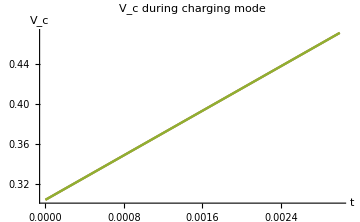
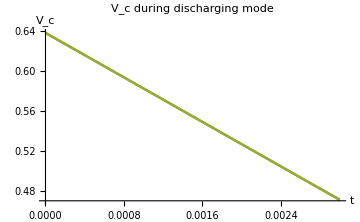
Charging period (t_lo) | Discharging period (t_hi)
{0.003,0.003,0.00299999} | {0.003,0.003,0.003}
Error over temp: 0.000264659% | Error over temp: 0.0000343231%
Full period (t_lo+t_hi) | 
{0.006,0.006,0.00599999} | Avg period: 0.006
Error over temp: 0.000149491% | 
-Graphics- | -Graphics-

```mathematica
Block[{Vdd=1, Vinv=0.471, Ut1=UtFunc[0],Ut2=UtFunc[25],Ut3=UtFunc[50], C1=1.5*10^-15,C2=300*10^-18,Iin=100 10^-15,γn=1.0,γp=1.0,tMax11, tMax12, tMax13, tMax21,tMax22,tMax23,ts},
tMax11=t/.Solve[VcCharge[t,Ut1,Iin,C1,C2,Vdd,Vinv,γn,γp]==Vinv, t]⟦1⟧;
tMax12=t/.Solve[VcCharge[t,Ut2,Iin,C1,C2,Vdd,Vinv,γn,γp]==Vinv, t]⟦1⟧;
tMax13=t/.Solve[VcCharge[t,Ut3,Iin,C1,C2,Vdd,Vinv,γn,γp]==Vinv, t]⟦1⟧;
tMax21=t/.Solve[VcDischarge[t,Ut1,Iin,C1,C2,Vdd,Vinv,γn,γp]==Vinv, t]⟦1⟧;
tMax22=t/.Solve[VcDischarge[t,Ut2,Iin,C1,C2,Vdd,Vinv,γn,γp]==Vinv, t]⟦1⟧;
tMax23=t/.Solve[VcDischarge[t,Ut3,Iin,C1,C2,Vdd,Vinv,γn,γp]==Vinv, t]⟦1⟧;
ts={tMax11, tMax12, tMax13}+{tMax21, tMax22, tMax23};
Grid[{
(*{{ Ut1,Ut2, Ut3},{ Vinv, Vdd}},*)
{Row[{"Charging period (t_lo)"}],Row[{"Discharging period (t_hi)"}]},
{{tMax11, tMax12, tMax13},{tMax21, tMax22, tMax23}},
{Row[{"Error over temp: ",(tMax11-tMax13)*100/Mean[{tMax11,tMax12,tMax13}], "%"}],Row[{"Error over temp: ",(tMax21-tMax23)*100/Mean[{tMax21,tMax22,tMax23}], "%"}]},
{Row[{"Full period (t_lo+t_hi)"}]},
{ts,Row[{"Avg period: ", Mean[ts]}]},
{Row[{"Error over temp: ", (ts⟦1⟧-ts⟦3⟧)*100/Mean[ts], "%"}]},
{
Show[
Plot[{
VcCharge[t,Ut1,Iin,C1,C2,Vdd,Vinv,γn,γp],
VcCharge[t,Ut2,Iin,C1,C2,Vdd,Vinv,γn,γp],
VcCharge[t,Ut3,Iin,C1,C2,Vdd,Vinv,γn,γp]},{t,0,tMax11}, 
ImageSize->Medium,PlotLabel->"V_c during charging mode",AxesLabel->{"t", "V_c"}]
],
Show[
Plot[{
VcDischarge[t,Ut1,Iin,C1,C2,Vdd,Vinv,γn,γp],
VcDischarge[t,Ut2,Iin,C1,C2,Vdd,Vinv,γn,γp],
VcDischarge[t,Ut3,Iin,C1,C2,Vdd,Vinv,γn,γp]},{t,0,tMax21},
ImageSize->Medium,PlotLabel->"V_c during discharging mode",AxesLabel->{"t", "V_c"}]
]}
}]
]
```

#### Varying Input Current

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

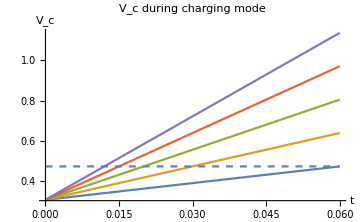
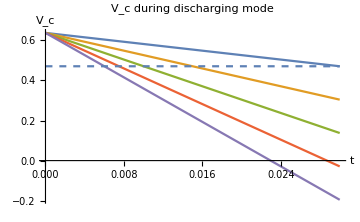
Charging period (t_lo) | Discharging period (t_hi)
{0.0599999} | {0.03}
Full period (t_lo+t_hi) | 
{0.0899999} | Avg period: 0.0899999
-Graphics- | -Graphics-

```mathematica
Block[{Vdd=1, Vinv=0.471, Ut2=UtFunc[25], C1=1.5*10^-15,C2=300*10^-18,Iin=100 10^-15,γn=1.0,γp=0.5,tMax11, tMax12, tMax13, tMax21,tMax22,tMax23,ts},
IinList={10^-14,10^-13,10^-12,10^-11,10^-10};
IinList=Range[5]*10^-14;
VcChargeTable =Re[Table[VcCharge[t,Ut2],{Iin,IinList}]];
VcDischargeTable =Re[Table[VcDischarge[t,Ut2],{Iin,IinList}]];
tMax12=t/.Solve[VcCharge[t,Ut2,Min[IinList],C1,C2,Vdd,Vinv,γn,γp]==Vinv, t]⟦1⟧;
tMax22=t/.Solve[VcDischarge[t,Ut2,Min[IinList],C1,C2,Vdd,Vinv,γn,γp]==Vinv, t]⟦1⟧;
ts={ tMax12}+{ tMax22};
Grid[{
{Row[{"Charging period (t_lo)"}],Row[{"Discharging period (t_hi)"}]},
{{tMax12},{tMax22}},
{Row[{"Full period (t_lo+t_hi)"}]},
{ts,Row[{"Avg period: ", Mean[ts]}]},
{
Show[
Plot[VcChargeTable,{t,0,tMax12}, 
ImageSize->Medium,PlotLabel->"V_c during charging mode",AxesLabel->{"t", "V_c"}],
Plot[Vinv,{t,0,tMax12}, PlotStyle->Dashed]
],
Show[
Plot[VcDischargeTable,{t,0,tMax22},
ImageSize->Medium,PlotLabel->"V_c during discharging mode",AxesLabel->{"t", "V_c"}],
Plot[Vinv,{t,0,tMax22}, PlotStyle->Dashed]
]}
}]
]
```

### Plot of T vs I_in

Note: All of these plots include leakage current because it’s the most accurate model of the circuit that I have derived

#### Varying Temperature

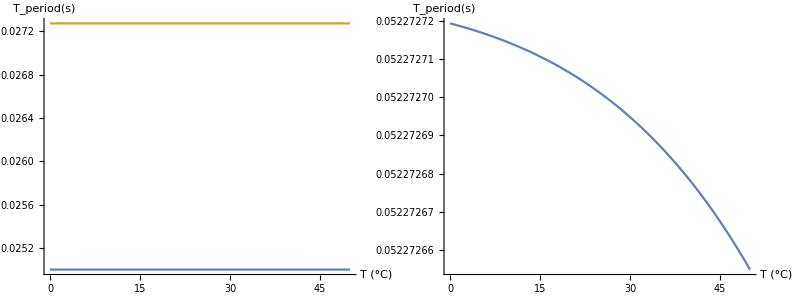

```mathematica
Block[{Vdd=1, Vinv=0.471, Ut=UtFunc[25], C1=1.5*10^-15,C2=300*10^-18,
Iin=10 10^-15,I0ch=1 10^-15,I0dch=1 10^-15,γn=1.0,γp=1.1,imgSz=300},
Grid[{{
Plot[{TCharge[UtFunc[temp],Iin,C1,C2,Vdd,Vinv,γn,γp,I0ch],TDischarge[UtFunc[temp],Iin,C1,C2,Vdd,Vinv,γn,γp,I0dch]},{temp,0,50},ImageSize->imgSz, AxesLabel->{"T (°C)","T_period(s)"}],
Plot[{TCharge[UtFunc[temp],Iin,C1,C2,Vdd,Vinv,γn,γp,I0ch]+TDischarge[UtFunc[temp],Iin,C1,C2,Vdd,Vinv,γn,γp,I0dch]},{temp,0,50},ImageSize->imgSz, AxesLabel->{"T (°C)","T_period(s)"}]

}}]
]
```

#### Varying Input Current

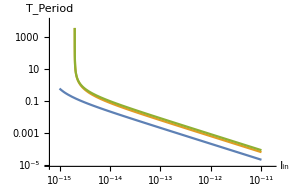
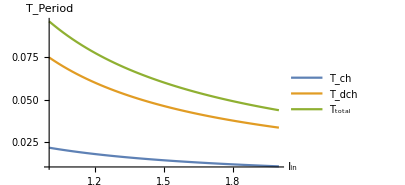
-Graphics- | -Graphics-

```mathematica
Block[{Vdd=1, Vinv=0.471, Ut=UtFunc[25], C1=1.5*10^-15,C2=300*10^-18,
Iin=10 10^-15,I0ch=-1 10^-15,I0dch=-1 10^-15,expPower=-14,γn=0.5,γp=1.5,imgSz=300},
Grid[{
{LogLogPlot[{
TCharge[Ut,Iin,C1,C2,Vdd,Vinv,γn,γp,I0ch],TDischarge[Ut,Iin,C1,C2,Vdd,Vinv,γn,γp,I0dch],
TCharge[Ut,Iin,C1,C2,Vdd,Vinv,γn,γp,I0ch]+TDischarge[Ut,Iin,C1,C2,Vdd,Vinv,γn,γp,I0dch]},
{Iin,10^-15,10^-11},ImageSize->imgSz,AxesLabel->{"I_in","T_Period"}],
Plot[{
TCharge[Ut,Iin,C1,C2,Vdd,Vinv,γn,γp,I0ch],TDischarge[Ut,Iin,C1,C2,Vdd,Vinv,γn,γp,I0dch],
TCharge[Ut,Iin,C1,C2,Vdd,Vinv,γn,γp,I0ch]+TDischarge[Ut,Iin,C1,C2,Vdd,Vinv,γn,γp,I0dch]},
{Iin,1 10^expPower,2 10^expPower},ImageSize->imgSz,AxesLabel->{"I_in","T_Period"},PlotLegends->{"T_ch","T_dch","T_total"}]}
}]
]
```

### Plot of F vs I_in

Note: All of these plots include leakage current because it’s the most accurate model of the circuit that I have derived

#### Varying Temperature

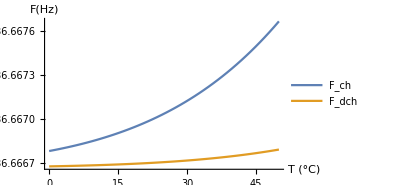
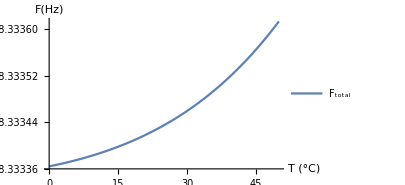
-Graphics- | -Graphics-

```mathematica
Block[{Vdd=1, Vinv=0.471, Ut=UtFunc[25], C1=1.5*10^-15,C2=300*10^-18,
Iin=100 10^-15,I0ch=1 10^-15,I0dch=1 10^-15,γn=1.0,γp=1.0,imgSz=300},
Grid[{{
Plot[{
1/TCharge[UtFunc[temp],Iin,C1,C2,Vdd,Vinv,γn,γp,I0ch],
1/TDischarge[UtFunc[temp],Iin,C1,C2,Vdd,Vinv,γn,γp,I0dch]},
{temp,0,50},ImageSize->imgSz, AxesLabel->{"T (°C)","F(Hz)"},PlotLegends->{"F_ch","F_dch"}],
Plot[{1/(TCharge[UtFunc[temp],Iin,C1,C2,Vdd,Vinv,γn,γp,I0ch]+TDischarge[UtFunc[temp],Iin,C1,C2,Vdd,Vinv,γn,γp,I0dch])},
{temp,0,50},ImageSize->imgSz, AxesLabel->{"T (°C)","F(Hz)"},PlotLegends->{"F_total"}]
}}]
]
```

#### Varying Input Current

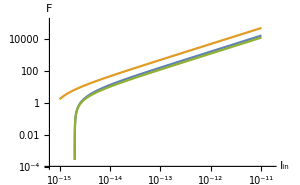
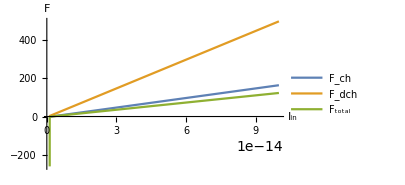
-Graphics- | -Graphics-

```mathematica
Block[{Vdd=1, Vinv=0.471, Ut=UtFunc[25], C1=1.5*10^-15,C2=300*10^-18,
Iin=10 10^-15,I0ch=-1 10^-15,I0dch=-1 10^-15,expPower=-15,γn=1.5,γp=0.5,imgSz=300},
Grid[{
{LogLogPlot[{
1/TCharge[Ut,Iin,C1,C2,Vdd,Vinv,γn,γp,I0ch],1/TDischarge[Ut,Iin,C1,C2,Vdd,Vinv,γn,γp,I0dch],
1/(TCharge[Ut,Iin,C1,C2,Vdd,Vinv,γn,γp,I0ch]+TDischarge[Ut,Iin,C1,C2,Vdd,Vinv,γn,γp,I0dch])},
{Iin,10^-15,10^-11},ImageSize->imgSz,AxesLabel->{"I_in","F"}],
Plot[{
1/TCharge[Ut,Iin,C1,C2,Vdd,Vinv,γn,γp,I0ch],1/TDischarge[Ut,Iin,C1,C2,Vdd,Vinv,γn,γp,I0dch],
1/(TCharge[Ut,Iin,C1,C2,Vdd,Vinv,γn,γp,I0ch]+TDischarge[Ut,Iin,C1,C2,Vdd,Vinv,γn,γp,I0dch])},
{Iin,1 10^expPower,100 10^expPower},ImageSize->imgSz,AxesLabel->{"I_in","F"},PlotLegends->{"F_ch","F_dch","F_total"}]}
}]
]
```

### Model of FI Curve assuming no leakage current

From above, we know that the charging and discharging periods are as written below:

T_ch=(C_1+C_2)/(I_in γ_p)ϕ_t Log[(ⅇ^((C_2 V_dd)/((C_1+C_2)ϕ_t))(γ_n +γ_p ⅇ^(V_inv/ϕ_t)))/(γ_n ⅇ^((C_2 V_dd)/((C_1+C_2)ϕ_t)) +γ_p ⅇ^(V_inv/ϕ_t))]
T_dch=(C_2 V_dd+(C_1+C_2) ϕ_t (Log[ γ_n+γ_p ⅇ^((-V_dd+V_inv)/ϕ_t) ]-Log[γ_n+γ_p ⅇ^((-(C_1 V_dd)/(C_1+C_2)+V_inv)/ϕ_t) ]))/(I_in γ_n)

If we can assume that V_dd, V_inv, γ_n,γ_p,C_1,and C_2 are constant for any given temperature, then we can rewrite the equations above as:
T_ch=α_ch/I_in
T_dch=α_dch/I_in
where α_ch and α_dch are constants for any given temperature.
∴ the overall period, T, of the oscillation is equal to the following equation
T=T_ch+T_dch
T=α_ch/I_in+α_dch/I_in
T=1/I_in(α_ch+α_dch)
This can be rewritten in terms of Frequency (as opposed to period) as follows:
F=I_in 1/(α_ch+α_dch)
F=m ·I_in
If we know that there is always some leakage current, then we can add that into the model as an offset to the input current:
F=m ·(I_in+I_0)

Full blown model of the frequency, based on complete forms of the charging and discharing periods.

```mathematica
F==FullSimplify[ 1/(TCharge[Ut,Iin,C1,C2,Vdd,Vinv,γn,γp]+TDischarge[Ut,Iin,C1,C2,Vdd,Vinv,γn,γp])]
```

F==(Iin γn γp)/(C2 Vdd γp+(C1+C2) Ut (γn Log[(ⅇ^((C2 Vdd)/((C1+C2) Ut)) (γn+ⅇ^(Vinv/Ut) γp))/(ⅇ^((C2 Vdd)/((C1+C2) Ut)) γn+ⅇ^(Vinv/Ut) γp)]+γp (Log[γn+ⅇ^((-Vdd+Vinv)/Ut) γp]-Log[γn+ⅇ^((-(C1 Vdd)/(C1+C2)+Vinv)/Ut) γp])))

### Model of FI Curve with leakage current

From above, we know that the charging and discharging periods are as written below:

T_ch=(C_2 V_dd+(C_1+C_2) ϕ_t (-Log[I_ch0+I_in (γ_n ⅇ^(((C_2 V_dd)/(C_1+C_2)-V_inv)/ϕ_t) +γ_p)]+Log[I_ch0+I_in (γ_n ⅇ^(-V_inv/ϕ_t) +γ_p)]))/(I_ch0+I_in γ_p)
T_dch=(C_2 V_dd+(C_1+C_2) ϕ_t (Log[I_dch0+I_in (γ_n+γ_p ⅇ^((-V_dd+V_inv)/ϕ_t) )]-Log[I_dch0+I_in (γ_n+γ_p ⅇ^((-(C_1 V_dd)/(C_1+C_2)+V_inv)/ϕ_t) )]))/(I_dch0+I_in γ_n)

If we can assume that V_dd, V_inv, γ_n,γ_p,C_1,and C_2 are constant for any given temperature, then we can rewrite the equations above as:
T_ch=(ρ_c1+ρ_c2 (-Log[I_ch0+I_in (γ_n ⅇ^(ρ_c1/ρ_c2)ⅇ^ρ_c3 +γ_p)]+Log[I_ch0+I_in (γ_n ⅇ^ρ_c3 +γ_p)]))/(I_ch0+I_in γ_p)
T_dch=(ρ_d1+ρ_d2 (Log[I_dch0+I_in (γ_n+γ_p ⅇ^ρ_d3 )]-Log[I_dch0+I_in (γ_n+γ_p ⅇ^(ρ_d1/ρ_d2)ⅇ^ρ_d3 )]))/(I_dch0+I_in γ_n)
where ρ_c1, ρ_c2,ρ_c3,ρ_d1, ρ_d2, and ρ_d3 are constants for any given temperature.
We can try to further simplify this to one logarithm for each equation, with 6 fitting parameters each.
T_ch=ρ_c2/(I_ch0+I_in γ_p)Log[(ⅇ^(ρ_c1/ρ_c2)(I_ch0+I_in (γ_n ⅇ^ρ_c3 +γ_p)))/(I_ch0+I_in (γ_n ⅇ^(ρ_c1/ρ_c2)ⅇ^ρ_c3 +γ_p))]
T_dch=ρ_d2/(I_dch0+I_in γ_n) Log[(ⅇ^(ρ_d1/ρ_d2)(I_dch0+I_in (γ_n+γ_p ⅇ^ρ_d3 )))/(I_dch0+I_in (γ_n+γ_p ⅇ^(ρ_d1/ρ_d2)ⅇ^ρ_d3 ))]
We notice that these two equations look essentially identical but will have different extraction parameters.  As such, we simplify the fitting function down to one equation, but will fit two sets of data, one for the charging period and one for the discharging period.
T_halfperiod=ρ_2/(ρ_4+I_in ρ_5)Log[(ⅇ^(ρ_1/ρ_2)(ρ_4+I_in (ρ_6 ⅇ^ρ_3 +ρ_5)))/(ρ_4+I_in (ρ_6 ⅇ^(ρ_1/ρ_2)ⅇ^ρ_3 +ρ_5))]

∴ The overall period, T, of the oscillation is equal to the following equation
T=T_ch+T_dch
T=ρ_c2/(I_ch0+I_in γ_p)Log[(ⅇ^(ρ_c1/ρ_c2)(I_ch0+I_in (γ_n ⅇ^ρ_c3 +γ_p)))/(I_ch0+I_in (γ_n ⅇ^(ρ_c1/ρ_c2)ⅇ^ρ_c3 +γ_p))]+ρ_d2/(I_dch0+I_in γ_n) Log[(ⅇ^(ρ_d1/ρ_d2)(I_dch0+I_in (γ_n+γ_p ⅇ^ρ_d3 )))/(I_dch0+I_in (γ_n+γ_p ⅇ^(ρ_d1/ρ_d2)ⅇ^ρ_d3 ))]
This can be rewritten in terms of Frequency (as opposed to period) as follows:
F=1/(ρ_c2/(I_ch0+I_in γ_p)Log[(ⅇ^(ρ_c1/ρ_c2)(I_ch0+I_in (γ_n ⅇ^ρ_c3 +γ_p)))/(I_ch0+I_in (γ_n ⅇ^(ρ_c1/ρ_c2)ⅇ^ρ_c3 +γ_p))]+ρ_d2/(I_dch0+I_in γ_n) Log[(ⅇ^(ρ_d1/ρ_d2)(I_dch0+I_in (γ_n+γ_p ⅇ^ρ_d3 )))/(I_dch0+I_in (γ_n+γ_p ⅇ^(ρ_d1/ρ_d2)ⅇ^ρ_d3 ))])

Full blown model of the frequency, based on complete forms of the charging and discharing periods.

```mathematica
F==FullSimplify[ 1/(TCharge[Ut,Iin,C1,C2,Vdd,Vinv,γn,γp,Ich0]+TDischarge[Ut,Iin,C1,C2,Vdd,Vinv,γn,γp,Idch0])]
```

F==1/((C2 Vdd+(C1+C2) Ut (-Log[Ich0+Iin (ⅇ^(((C2 Vdd)/(C1+C2)-Vinv)/Ut) γn+γp)]+Log[Ich0+Iin (ⅇ^(-Vinv/Ut) γn+γp)]))/(Ich0+Iin γp)+(C2 Vdd+(C1+C2) Ut (Log[Idch0+Iin (γn+ⅇ^((-Vdd+Vinv)/Ut) γp)]-Log[Idch0+Iin (γn+ⅇ^((-(C1 Vdd)/(C1+C2)+Vinv)/Ut) γp)]))/(Idch0+Iin γn))

```mathematica
Solve[F==1/(TCharge[Ut,Iin,C1,C2,Vdd,Vinv,γn,γp,Ich0]+TDischarge[Ut,Iin,C1,C2,Vdd,Vinv,γn,γp,Idch0]),Iin]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[F==1/((C2 Vdd+(C1+C2) Ut (-Log[Ich0+Iin (ⅇ^(((C2 Vdd)/(C1+C2)-Vinv)/Ut) γn+γp)]+Log[Ich0+Iin (ⅇ^(-Vinv/Ut) γn+γp)]))/(Ich0+Iin γp)+(C2 Vdd+(C1+C2) Ut (Log[Idch0+Iin (γn+ⅇ^((-Vdd+Vinv)/Ut) γp)]-Log[Idch0+Iin (γn+ⅇ^((-(C1 Vdd)/(C1+C2)+Vinv)/Ut) γp)]))/(Idch0+Iin γn)),Iin]

## Solve AH Dynamics with Feedback

### Solve charging dynamical equation with feedback

```mathematica
FullSimplify[DSolve[{(C1+C2)/Iin Vc'[t]==1+ⅇ^((-Vc[t])/Ut)+I0/Iin ⅇ^(Vc[t]/Ut),Vc[0]==Vinv-C2/(C1+C2)Vdd},Vc[t],t]]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Vc[t]→Ut Log[(-Iin+√(4 I0-Iin) √Iin Tan[(√(4 I0-Iin) √Iin t)/(2 C1 Ut+2 C2 Ut)+ArcTan[(2 ⅇ^((-(C2 Vdd)/(C1+C2)+Vinv)/Ut) I0+Iin)/(√(4 I0-Iin) √Iin)]])/(2 I0)]}}

```mathematica
VcChargeFB[t_,Ut_]:=Ut Log[(-Iin+√(4 I0-Iin) √Iin Tan[(√(4 I0-Iin) √Iin t)/(2 C1 Ut+2 C2 Ut)+ArcTan[(2 ⅇ^((-(C2 Vdd)/(C1+C2)+Vinv)/Ut) I0+Iin)/(√(4 I0-Iin) √Iin)]])/(2 I0)]
VcChargeFB[t_,Ut_,Iin_,I0_,C1_,C2_,Vdd_,Vinv_]:=Ut Log[(-Iin+√(4 I0-Iin) √Iin Tan[(√(4 I0-Iin) √Iin t)/(2 C1 Ut+2 C2 Ut)+ArcTan[(2 ⅇ^((-(C2 Vdd)/(C1+C2)+Vinv)/Ut) I0+Iin)/(√(4 I0-Iin) √Iin)]])/(2 I0)]
```

### Integrate charging dynamical equation to get period measurement (with feedback)

```mathematica
FullSimplify[Integrate[(C1+C2)/(Iin (1+ⅇ^(-Vc/Ut)+I0/Iin ⅇ^(Vc[t]/Ut))),{Vc, Vinv-C2/(C1+C2)Vdd,Vinv}, Assumptions->{C1>0, C2>0, Iin>0, I0>0,Ut>0, Vdd>0, Vinv>0}]]
```

(C1+C2) ((Ut Log[Iin+ⅇ^(Vinv/Ut) (ⅇ^(((-Vc+Vinv)[t])/Ut) I0+Iin)])/(ⅇ^(((-Vc+Vinv)[t])/Ut) I0+Iin)-(Ut Log[ⅇ^(-(C2 Vdd)/((C1+C2) Ut)) (ⅇ^((C2 Vdd)/((C1+C2) Ut)) Iin+ⅇ^(Vinv/Ut) (ⅇ^(((Vc-(C2 Vdd)/(C1+C2)+Vinv)[t])/Ut) I0+Iin))])/(ⅇ^(((Vc-(C2 Vdd)/(C1+C2)+Vinv)[t])/Ut) I0+Iin))

```mathematica
TChargeFB[Ut_]:=(C1+C2) ((Ut Log[Iin+ⅇ^(Vinv/Ut) (ⅇ^(((-Vc+Vinv)[t])/Ut) I0+Iin)])/(ⅇ^(((-Vc+Vinv)[t])/Ut) I0+Iin)-(Ut Log[ⅇ^(-(C2 Vdd)/((C1+C2) Ut)) (ⅇ^((C2 Vdd)/((C1+C2) Ut)) Iin+ⅇ^(Vinv/Ut) (ⅇ^(((Vc-(C2 Vdd)/(C1+C2)+Vinv)[t])/Ut) I0+Iin))])/(ⅇ^(((Vc-(C2 Vdd)/(C1+C2)+Vinv)[t])/Ut) I0+Iin))
TChargeFB[Ut_,Iin_,C1_,C2_,Vdd_,Vinv_]:=(C1+C2) ((Ut Log[Iin+ⅇ^(Vinv/Ut) (ⅇ^(((-Vc+Vinv)[t])/Ut) I0+Iin)])/(ⅇ^(((-Vc+Vinv)[t])/Ut) I0+Iin)-(Ut Log[ⅇ^(-(C2 Vdd)/((C1+C2) Ut)) (ⅇ^((C2 Vdd)/((C1+C2) Ut)) Iin+ⅇ^(Vinv/Ut) (ⅇ^(((Vc-(C2 Vdd)/(C1+C2)+Vinv)[t])/Ut) I0+Iin))])/(ⅇ^(((Vc-(C2 Vdd)/(C1+C2)+Vinv)[t])/Ut) I0+Iin))
```

### Solve discharging dynamical equation with feedback

```mathematica
FullSimplify[DSolve[{(C1+ C2)/Iin Vc'[t]==-1-ⅇ^((-(Vdd-Vc[t]))/Ut)-I0/Iin ⅇ^((Vdd-Vc[t])/Ut),Vc[0]==Vinv+C2/(C1+C2)Vdd},Vc[t],t]]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Vc[t]→Ut Log[-(ⅇ^(Vdd/Ut) (√Iin+√(4 I0-Iin) Tan[(√(4 I0-Iin) √Iin t)/(2 C1 Ut+2 C2 Ut)-ArcTan[(ⅇ^(-Vdd/Ut) (ⅇ^(Vdd/Ut)+2 ⅇ^(((C2 Vdd)/(C1+C2)+Vinv)/Ut)) √Iin)/(√(4 I0-Iin))]]))/(2 √Iin)]}}

```mathematica
VcDischargeFB[t_,Ut_]:=Ut Log[-(ⅇ^(Vdd/Ut) (√Iin+√(4 I0-Iin) Tan[(√(4 I0-Iin) √Iin t)/(2 C1 Ut+2 C2 Ut)-ArcTan[(ⅇ^(-Vdd/Ut) (ⅇ^(Vdd/Ut)+2 ⅇ^(((C2 Vdd)/(C1+C2)+Vinv)/Ut)) √Iin)/(√(4 I0-Iin))]]))/(2 √Iin)]
VcDischargeFB[t_,Ut_,Iin_,I0_,C1_,C2_,Vdd_,Vinv_]:=Ut Log[-(ⅇ^(Vdd/Ut) (√Iin+√(4 I0-Iin) Tan[(√(4 I0-Iin) √Iin t)/(2 C1 Ut+2 C2 Ut)-ArcTan[(ⅇ^(-Vdd/Ut) (ⅇ^(Vdd/Ut)+2 ⅇ^(((C2 Vdd)/(C1+C2)+Vinv)/Ut)) √Iin)/(√(4 I0-Iin))]]))/(2 √Iin)]
```

### Integrate discharging dynamical equation to get period measurement (with feedback)

```mathematica
FullSimplify[Integrate[-(C1+C2)/(Iin (1+ⅇ^((-(Vdd-Vc))/Ut)+I0/Iin ⅇ^((Vdd-Vc)/Ut))),{Vc, Vinv+C2/(C1+C2)Vdd, Vinv}, Assumptions->{C1>0, C2>0, Iin>0,I0>0, Ut>0, Vdd>0, Vinv>0}]]
```

-(2 (C1+C2) Ut (ArcTan[(ⅇ^(-Vdd/Ut) (ⅇ^(Vdd/Ut)+2 ⅇ^(Vinv/Ut)))/(√(-1+(4 I0)/Iin))]-ArcTan[(ⅇ^(-Vdd/Ut) (ⅇ^(Vdd/Ut)+2 ⅇ^(((C2 Vdd)/(C1+C2)+Vinv)/Ut)))/(√(-1+(4 I0)/Iin))]))/(√(-1+(4 I0)/Iin) Iin)

```mathematica
TDischargeFB[Ut_]:=-(2 (C1+C2) Ut (ArcTan[(ⅇ^(-Vdd/Ut) (ⅇ^(Vdd/Ut)+2 ⅇ^(Vinv/Ut)))/(√(-1+(4 I0)/Iin))]-ArcTan[(ⅇ^(-Vdd/Ut) (ⅇ^(Vdd/Ut)+2 ⅇ^(((C2 Vdd)/(C1+C2)+Vinv)/Ut)))/(√(-1+(4 I0)/Iin))]))/(√(-1+(4 I0)/Iin) Iin)
TDischargeFB[Ut_,Iin_,I0_,C1_,C2_,Vdd_,Vinv_]:=-(2 (C1+C2) Ut (ArcTan[(ⅇ^(-Vdd/Ut) (ⅇ^(Vdd/Ut)+2 ⅇ^(Vinv/Ut)))/(√(-1+(4 I0)/Iin))]-ArcTan[(ⅇ^(-Vdd/Ut) (ⅇ^(Vdd/Ut)+2 ⅇ^(((C2 Vdd)/(C1+C2)+Vinv)/Ut)))/(√(-1+(4 I0)/Iin))]))/(√(-1+(4 I0)/Iin) Iin)
```

### Plot of V_c waveform with feedback

#### Varying Temperature

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

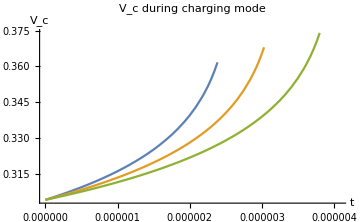
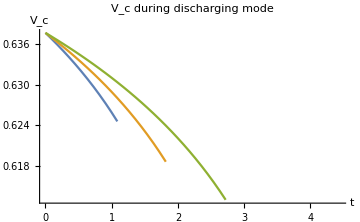
Charging period (t_lo) | Discharging period (t_hi)
{2.65357×10^-6+0. ⅈ,3.30038×10^-6+0. ⅈ,4.07591×10^-6+0. ⅈ} | {2.67824×10^-7+0. ⅈ,3.46381×10^-7+0. ⅈ,4.443×10^-7+0. ⅈ}
Error over temp: -42.5431+0. ⅈ% | Error over temp: -50.0167+0. ⅈ%
Full period (t_lo+t_hi) | 
{2.9214×10^-6+0. ⅈ,3.64676×10^-6+0. ⅈ,4.52021×10^-6+0. ⅈ} | Avg period: 3.69612×10^-6+0. ⅈ
Error over temp: -43.2566+0. ⅈ% | 
-Graphics- | -Graphics-

```mathematica
Block[{Vdd=1, Vinv=0.471, Ut1=UtFunc[20],Ut2=UtFunc[25],Ut3=UtFunc[30], C1=1.5*10^-15,C2=300*10^-18, Iin=100*10^-15,I0=0.1 10^-15,tMax11, tMax12, tMax13, tMax21,tMax22,tMax23,ts},
tMax11=t/.Solve[VcChargeFB[t,Ut1]==Vinv, t]⟦1⟧;
tMax12=t/.Solve[VcChargeFB[t,Ut2]==Vinv, t]⟦1⟧;
tMax13=t/.Solve[VcChargeFB[t,Ut3]==Vinv, t]⟦1⟧;
tMax21=t/.Solve[VcDischargeFB[t,Ut1]==Vinv, t]⟦1⟧;
tMax22=t/.Solve[VcDischargeFB[t,Ut2]==Vinv, t]⟦1⟧;
tMax23=t/.Solve[VcDischargeFB[t,Ut3]==Vinv, t]⟦1⟧;
ts={tMax11, tMax12, tMax13}+{tMax21, tMax22, tMax23};
Grid[{
(*{{ Ut1,Ut2, Ut3},{ Vinv, Vdd}},*)
{Row[{"Charging period (t_lo)"}],Row[{"Discharging period (t_hi)"}]},
{{tMax11, tMax12, tMax13},{tMax21, tMax22, tMax23}},
{Row[{"Error over temp: ",(tMax11-tMax13)*100/Mean[{tMax11,tMax12,tMax13}], "%"}],Row[{"Error over temp: ",(tMax21-tMax23)*100/Mean[{tMax21,tMax22,tMax23}], "%"}]},
{Row[{"Full period (t_lo+t_hi)"}]},
{ts,Row[{"Avg period: ", Mean[ts]}]},
{Row[{"Error over temp: ", (ts⟦1⟧-ts⟦3⟧)*100/Mean[ts], "%"}]},
{
Show[
Plot[{VcChargeFB[t,Ut1],VcChargeFB[t,Ut2],VcChargeFB[t,Ut3]},{t,0,tMax13}, 
ImageSize->Medium,PlotLabel->"V_c during charging mode",AxesLabel->{"t", "V_c"}]
],
Show[
Plot[{VcDischargeFB[t,Ut1],VcDischargeFB[t,Ut2],VcDischargeFB[t,Ut3]},{t,0,tMax23},
ImageSize->Medium,PlotLabel->"V_c during discharging mode",AxesLabel->{"t", "V_c"}]
]}
}]
]
```

#### Varying Input Current

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

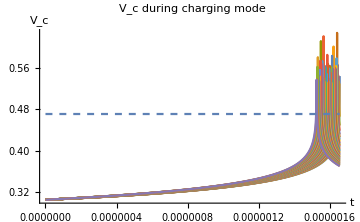
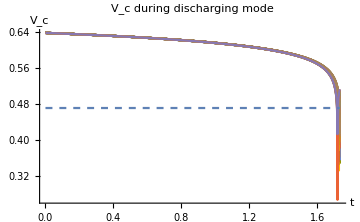
Charging period (t_lo) | Discharging period (t_hi)
{1.65581×10^-6} | {1.73252×10^-7}
Full period (t_lo+t_hi) | 
{1.82907×10^-6} | Avg period: 1.82907×10^-6
-Graphics- | -Graphics-

```mathematica
Block[{Vdd=1,Vinv=0.471,Ut1=UtFunc[20],Ut2=UtFunc[25],Ut3=UtFunc[30],C1=1.5*10^-15,C2=300*10^-18, Iin=10*10^-15,I0=0.2 10^-15,tMax11,tMax12,tMax13,tMax21,tMax22,tMax23,ts},
IinList={10^-14,10^-13,10^-12,10^-11,10^-10};
IinList=Range[50]*10^-13;
VcChargeTable =Re[Table[VcChargeFB[t,Ut2],{Iin,IinList}]];
VcDischargeTable =Re[Table[VcDischargeFB[t,Ut2],{Iin,IinList}]];
tMax12s=Re[t/.Solve[VcChargeFB[t,Ut2,#,I0,C1,C2,Vdd,Vinv]==Vinv, t]⟦1⟧&/@IinList];
tMax22s=Re[t]/.Solve[VcDischargeFB[t,Ut2,#,I0,C1,C2,Vdd,Vinv]==Vinv, t]⟦1⟧&/@IinList;
tMax12=Re[t/.Solve[VcChargeFB[t,Ut2]==Vinv, t]⟦1⟧];
tMax22=Re[t/.Solve[VcDischargeFB[t,Ut2]==Vinv, t]⟦1⟧];
(*tMax12=Re[t/.(Solve[#==Vinv, t]&/@VcChargeTable)⟦1⟧];*)
ts={tMax12}+{tMax22};
Grid[{
(*{{ Ut1,Ut2, Ut3},{ Vinv, Vdd}},*)
{Row[{"Charging period (t_lo)"}],Row[{"Discharging period (t_hi)"}]},
{{tMax12},{ tMax22}},
{Row[{"Full period (t_lo+t_hi)"}]},
{ts,Row[{"Avg period: ", Mean[ts]}]},
{
Show[
Plot[{VcChargeTable},{t,0,tMax12}, 
ImageSize->Medium,PlotLabel->"V_c during charging mode",
AxesLabel->{"t", "V_c"},(*PlotLegends->IinList,*) PlotRange->All],
Plot[Vinv,{t,0,tMax12}, PlotStyle->Dashed]
],
Show[
Plot[{VcDischargeTable},{t,0,tMax22},
ImageSize->Medium,PlotLabel->"V_c during discharging mode",
AxesLabel->{"t", "V_c"}, PlotRange->All],
Plot[Vinv,{t,0,tMax22}, PlotStyle->Dashed]
]}
}]
]
```

### Plot of T vs I_in

#### Varying Temperature

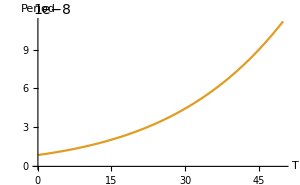

```mathematica
Block[{Vdd=1, Vinv=0.471, Ut=UtFunc[25], C1=1.5*10^-15,C2=300*10^-18,
Iin=10 10^-15,I0=1 10^-15,imgSz=300},
Grid[{{
Plot[{TChargeFB[UtFunc[temp],Iin,I0,C1,C2,Vdd,Vinv],TDischargeFB[UtFunc[temp],Iin,I0,C1,C2,Vdd,Vinv]},{temp,0,50},ImageSize->imgSz,AxesLabel->{"T", "Period"}]
}}]
]
```

Note: This plot shows that the period varies dramatically over temperature (by one order of magnitude over 50C).

#### Varying Input Current

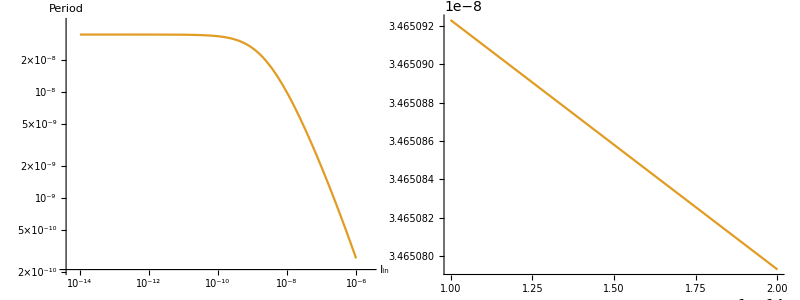

```mathematica
Block[{Vdd=1, Vinv=0.471, Ut=UtFunc[25], C1=1.5*10^-15,C2=300*10^-18,
Iin=100 10^-15,I0=1 10^-15,expPower=-14,imgSz=300},
Grid[{
{LogLogPlot[{TChargeFB[Ut,Iin,I0,C1,C2,Vdd,Vinv],TDischargeFB[Ut,Iin,I0,C1,C2,Vdd,Vinv]},{Iin,10^-14,10^-6},ImageSize->imgSz,AxesLabel->{"I_in", "Period"}],
Plot[{TChargeFB[Ut,Iin,I0,C1,C2,Vdd,Vinv],TDischargeFB[Ut,Iin,I0,C1,C2,Vdd,Vinv]},{Iin,1 10^expPower,2 10^expPower},ImageSize->imgSz]}
}]
]
```

The Period vs Input current plot for a circuit with feedback shows that having feedback will dominate the period of the oscillation for small input currents.  For large input currents, the period is dominated by charging of the cap using the input current.

## Appendix